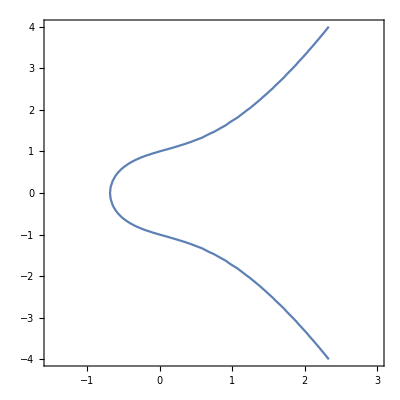

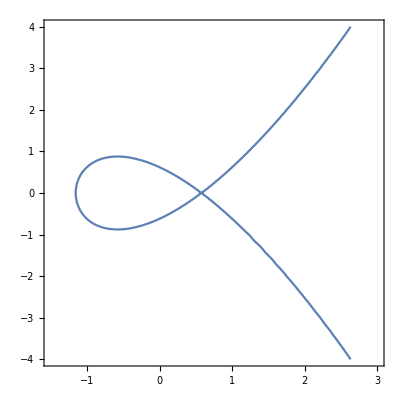

```mathematica
ContourPlot[y^2== x^3+x+1, {x,-1.5,3}, {y,-4,4}]
ContourPlot[y^2== x^3-x+2/Sqrt[27], {x,-1.5,3}, {y,-4,4}]
```

```mathematica
ec[x_] = Sqrt[x^3 +  x + 1]
ecsum[x1_,y1_,x2_,y2_] = {((y2-y1)/(x2-x1))^2-x1-x2,(y2-y1)/(x2-x1) ( x1-((y2-y1)/(x2-x1))^2-x1-x2)-y1}
(* fix there is a bug *=
```